```mathematica
exp=FullSimplify[MatrixExp[-I*ti*{{Nat*chi/2-deltaB,-Nat*chi/2},
{Nat*chi/2,-Nat*chi/2-deltaA}}]]
expconj=FullSimplify[MatrixExp[I*ti*{{Nat*chi/2-deltaB,-Nat*chi/2},
{Nat*chi/2,-Nat*chi/2-deltaA}}]]
```

{{(ⅇ^(1/2 ⅈ (deltaA+deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (-deltaA+deltaB-chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))+ⅇ^(1/2 ⅈ (deltaA+deltaB-√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (deltaA-deltaB+chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))))/(2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))),(ⅈ chi ⅇ^(1/2 ⅈ (deltaA+deltaB) ti) Nat Sin[1/2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti])/(√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))},{-(ⅈ chi ⅇ^(1/2 ⅈ (deltaA+deltaB) ti) Nat Sin[1/2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti])/(√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))),(ⅇ^(1/2 ⅈ (deltaA+deltaB-√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (-deltaA+deltaB-chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))+ⅇ^(1/2 ⅈ (deltaA+deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (deltaA-deltaB+chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))))/(2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))}}

{{(ⅇ^(-1/2 ⅈ (deltaA+deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (-deltaA+deltaB-chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))+ⅇ^(1/2 ⅈ (-deltaA-deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (deltaA-deltaB+chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))))/(2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))),-(ⅈ chi ⅇ^(-1/2 ⅈ (deltaA+deltaB) ti) Nat Sin[1/2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti])/(√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))},{(ⅈ chi ⅇ^(-1/2 ⅈ (deltaA+deltaB) ti) Nat Sin[1/2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti])/(√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))),(ⅇ^(1/2 ⅈ (-deltaA-deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (-deltaA+deltaB-chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))+ⅇ^(-1/2 ⅈ (deltaA+deltaB+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))) ti) (deltaA-deltaB+chi Nat+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))))/(2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)))}}

```mathematica
MatrixForm[%3]
```

%3

```mathematica
FullSimplify[exp[[1,2]]expconj[[1,2]]] (* these are the occupations n1 and n2 *)
FullSimplify[%/.{deltaA->-Nat chi/2,deltaB->Nat chi/2}]
```

(chi^2 Nat^2 Sin[1/2 √((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]^2)/((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))

Sinh[(chi Nat ti)/2]^2

```mathematica
Sin[-I*x]
```

-ⅈ Sinh[x]

-(chi Nat Sinh[√2 √(chi^2 Nat^2)])/(2 √2 √(chi^2 Nat^2))

```mathematica
FullSimplify[(exp[[2,1]]+I*exp[[1,1]])(expconj[[2,1]]-I*expconj[[1,1]])];
(* this is var(SxA - SyB) *)
```

```mathematica
%19
```

```mathematica
FullSimplify[((deltaA-deltaB+chi Nat)^2-chi Nat (chi Nat Cos[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) Sin[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]))/((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))]
```

```mathematica
((deltaA-deltaB+chi Nat)^2-chi Nat (chi Nat Cos[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) Sin[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]))/((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))
FullSimplify[%/.{deltaA->-Nat chi/2,deltaB->Nat chi/2}]
```

((deltaA-deltaB+chi Nat)^2-chi Nat (chi Nat Cos[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]+√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) Sin[√((deltaA-deltaB) (deltaA-deltaB+2 chi Nat)) ti]))/((deltaA-deltaB) (deltaA-deltaB+2 chi Nat))

ⅇ^(-chi Nat ti)

```mathematica
Cos[I*x]
```

Cosh[x]

```mathematica
FullSimplify[%/.{deltaA->-Nat chi/2,deltaB->Nat chi/2}]
```

ⅇ^(-chi Nat ti)

1. Cos[√(-1. chi^2 Nat^2) ti]-(1. chi Nat Sin[√(-1. chi^2 Nat^2) ti])/(√(-1. chi^2 Nat^2))

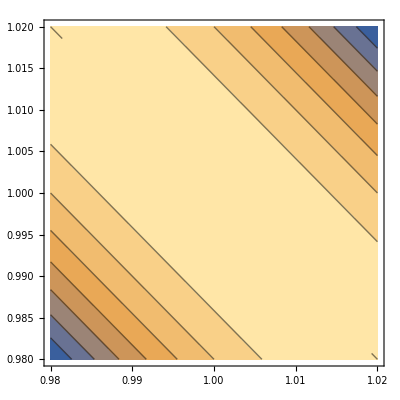

```mathematica
ContourPlot[Re[1/((-4+a+b) (a+b))((-2+a+b)^2-4 Cos[1/2 √((-4+a+b) (a+b)) chi Nat ti]-2 √((-4+a+b) (a+b)) Sin[1/2 √((-4+a+b) (a+b)) chi Nat ti])],{a,0.98,1.02},{b,0.98,1.02}]
```

2

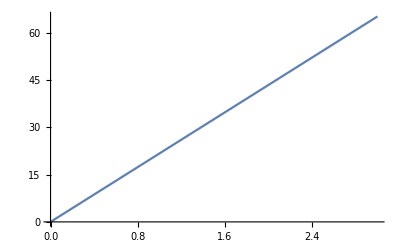

```mathematica
a=1+1

Plot[-10*Log10[(4-a^2+4*Cosh[2.5*ti*a]-2*a*Sinh[2.5*ti*a])/a^2],{ti,0,3}]
```

```mathematica
Nat =10000;
chi=0.0005;
Animate[Plot[-10*Log10[(4-a^2+4*Cosh[2.5*ti*a]-2*a*Sinh[2.5*ti*a])/a^2],{a,1,3.9}],{ti,0,2},AnimationRunning->False]
```

```mathematica
Derivative
```

```mathematica
D[1/((-4+a+b) (a+b))((-2+a+b)^2-4 Cos[1/2 √((-4+a+b) (a+b)) chi Nat ti]-2 √((-4+a+b) (a+b)) Sin[1/2 √((-4+a+b) (a+b)) chi Nat ti]), a]
```

```mathematica
FullSimplify[-1/((-4+a+b) (a+b)^2)((-2+a+b)^2-4 Cos[2.5 √((-4+a+b) (a+b)) ti]-2 √((-4+a+b) (a+b)) Sin[2.5 √((-4+a+b) (a+b)) ti])-1/((-4+a+b)^2 (a+b))((-2+a+b)^2-4 Cos[2.5 √((-4+a+b) (a+b)) ti]-2 √((-4+a+b) (a+b)) Sin[2.5 √((-4+a+b) (a+b)) ti])+1/((-4+a+b) (a+b))(2 (-2+a+b)-2.5 (-4+2 a+2 b) ti Cos[2.5 √((-4+a+b) (a+b)) ti]-((-4+2 a+2 b) Sin[2.5 √((-4+a+b) (a+b)) ti])/(√((-4+a+b) (a+b)))+(5. (-4+2 a+2 b) ti Sin[2.5 √((-4+a+b) (a+b)) ti])/(√((-4+a+b) (a+b))))
```